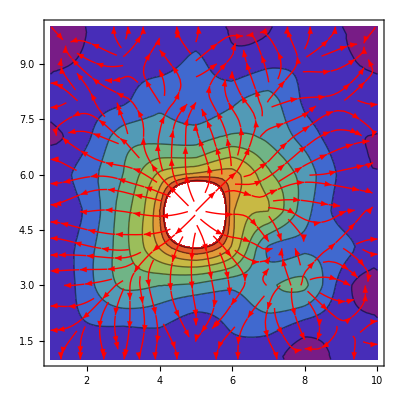

```mathematica
x1=10;
y1=10;
d=Table[0,{i,1,y1},{j,1,x1}];
c=0;
Do[{a=Table[0,{i,1,y1},{j,1,x1}];(*assume a disease free population*)
{a1,a2}={5,5};(*origin of the disease *)
lp=ListPlot[{{a1,a2}},PlotStyle->{Red,Thickness[0.01]}];(* marked origin of the disease *)
Do[{a[[a2]][[a1]]=a[[a2]][[a1]]+0.1,{a2,a1}=RandomChoice[{{a2-1,a1-1},{a2-1,a1},{a2-1,a1+1},{a2,a1-1},{a2,a1+1},{a2+1,a1-1},{a2+1,a1},{a2+1,a1+1}}](*random 8 move choices a king can make while moving from a point *)};If[a1==1 ||a2==1 ||a1==x1 ||a2==y1,Break[]],{n,1,100000}(*break at the boundary*)],
d=a+d,c=c+1},{i,1,50}](*inner loop updates the value of the position of the king(here it takes 100k steps) and the outer loop adds all possible(in this case 100) random paths the king takes the sum is done so that repeating placements of a king can be taken in consideration *)
u=ListInterpolation[d];
f1=ContourPlot[u[x,y],{x,1,x1},{y,1,y1},ColorFunction->"Rainbow"];
l=Grad[u[x,y],{x,y}];
f2=StreamPlot[{-l[[1]],-l[[2]]},{x,1,x1},{y,1,y1},StreamStyle->Red,StreamPoints->100];
Show[f1,f2]
```